## Solving a differential equation

You learned how to do this using undetermined coefficients, variation of parameters, or Laplace transforms.

```mathematica
ySoln[x_] = y[x]/.DSolve[{y''[x]+2 y'[x]+10 y[x]== x^2 Cos[5x]Exp[-x],
y[0]==0, y'[0]==0},y[x],x][[1]]//FullSimplify
```

1/512 ⅇ^-x ((21-32 x^2) cos(5 x)+40 x sin(5 x)-21 cos(3 x))

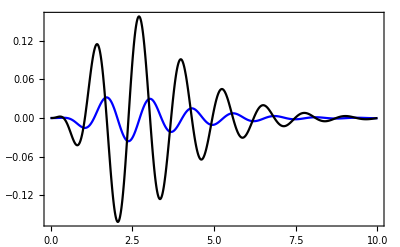

```mathematica
Plot[{ySoln[x],ySoln'[x]},{x,0,10},PlotRange->All,PlotStyle->{Blue,Black}]
```

## Solving linear systems

```mathematica
A={
{2,-1,0,0,0},
{-1,2,-1,0,0},
{0,-1,2,-1,0},
{0,0,-1,2,-1},
{0,0,0,-1,2}
}
```

(2 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 2 | -1
0 | 0 | 0 | -1 | 2)

```mathematica
b = {1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
LinearSolve[A,b]
```

{35/6,32/3,27/2,40/3,55/6}

```mathematica
B = RandomReal[{-1,1},{10,10}]
```

(0.0191295 | 0.42459 | -0.180924 | -0.460399 | 0.415324 | 0.112529 | 0.0765658 | -0.0903558 | -0.534519 | -0.950716
-0.431605 | 0.865099 | -0.515338 | 0.787466 | -0.278787 | 0.00830281 | -0.741636 | -0.0664537 | 0.329288 | -0.549452
-0.967466 | -0.136167 | -0.761581 | -0.167768 | 0.242726 | -0.583095 | 0.515528 | 0.726479 | -0.385267 | -0.10546
-0.389432 | -0.364813 | -0.515024 | -0.552987 | -0.228337 | -0.132333 | -0.0956529 | -0.213952 | 0.762442 | -0.856051
-0.600789 | -0.291433 | -0.616595 | 0.541801 | 0.279493 | -0.551261 | -0.135661 | 0.758986 | -0.521549 | -0.147749
-0.519276 | 0.636251 | -0.684934 | -0.181365 | -0.752811 | -0.446879 | -0.0259831 | -0.359453 | -0.62903 | 0.6272
-0.269847 | 0.678225 | 0.697205 | 0.64745 | 0.0357412 | 0.68068 | 0.493512 | -0.586147 | -0.410038 | 0.943179
0.852617 | 0.532557 | -0.532649 | -0.802182 | -0.91186 | -0.236029 | 0.669484 | 0.659281 | -0.603184 | -0.0360286
0.984224 | -0.178092 | 0.805811 | -0.876806 | 0.626351 | -0.151684 | -0.542902 | -0.698126 | 0.246802 | 0.79984
0.72862 | 0.340932 | 0.93675 | -0.294196 | 0.739804 | 0.834496 | 0.747242 | 0.0428391 | -0.631997 | 0.0985011)

```mathematica
c = RandomReal[{-1,1},{10}]
```

{0.720287,-0.777256,0.986366,-0.724023,-0.667342,0.0712201,0.803464,-0.731459,-0.42309,-0.0517947}

```mathematica
LinearSolve[B,c]
```

{-8.12513,2.96391,18.5094,-3.3965,-7.24297,-9.02754,-2.16829,4.55606,-2.12237,-5.12202}

## Finding eigenvalues

```mathematica
Eigenvalues[A]
```

{2+√3,3,2,1,2-√3}

```mathematica
Eigenvalues[B]
```

{1.14788+1.33798 ⅈ,1.14788-1.33798 ⅈ,-0.0939029+1.75105 ⅈ,-0.0939029-1.75105 ⅈ,-1.43677+0.486654 ⅈ,-1.43677-0.486654 ⅈ,0.931071+0. ⅈ,0.508+0. ⅈ,0.11345+0.0290694 ⅈ,0.11345-0.0290694 ⅈ}

## Solving a system of differential equations

Equations for two coupled oscillators with damping (two connected spring-mass systems or LRC circuits)

```mathematica
{uSoln[t_],vSoln[t_]}={u[t],v[t]}/.DSolve[
{u''[t]==-2u[t]+v[t]-1/2u'[t],
v''[t]==u[t] - 2v[t]-1/2 v'[t],
u[0]==1, v[0]==-1/2, u'[0]==0,v'[0]==0},{u[t],v[t]},t][[1]]//FullSimplify
```

{1/2820 ⅇ^(-t/4) (47 √15 sin((√15 t)/4)+45 √47 sin((√47 t)/4)+705 cos((√15 t)/4)+2115 cos((√47 t)/4)),(ⅇ^(-t/4) (47 √15 sin((√15 t)/4)+705 cos((√15 t)/4)-45 (√47 sin((√47 t)/4)+47 cos((√47 t)/4))))/2820}

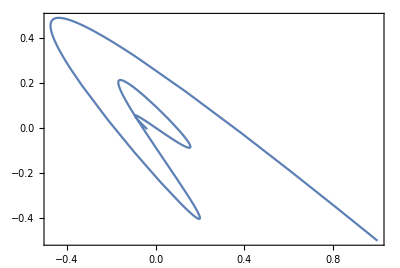

```mathematica
ParametricPlot[{uSoln[t],vSoln[t]},{t,0,10},PlotRange->All]
```

## Fourier series for rectified cosine

```mathematica
f[t_]=Piecewise[{{Cos[t],Abs[t]<Pi/2}}]
```

Piecewise[{{cos(t), Abs[t]<π/2}, {0, True}}]

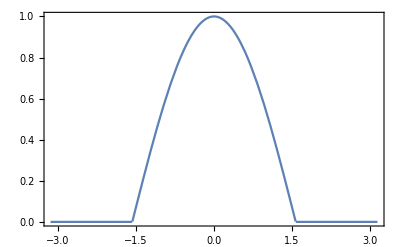

```mathematica
Plot[f[t],{t,-Pi,Pi}]
```

```mathematica
Subscript[A, n_]=1/Pi Integrate[f[t]Cos[n t],{t,-Pi,Pi}]
```

-(2 cos((π n)/2))/(π (n^2-1))

```mathematica
Subscript[A, 1]=Limit[Subscript[A, n],n->1]
```

1/2

```mathematica
fSum[M_,t_]:=Subscript[A, 0]/2 + Sum[Subscript[A, n] Cos[n t],{n,1,M}]
```

```mathematica
f4[t_]=fSum[4,t]
```

(cos(t))/2+(2 cos(2 t))/(3 π)-(2 cos(4 t))/(15 π)+1/π

```mathematica
f8[t_]=fSum[8,t]
```

(cos(t))/2+(2 cos(2 t))/(3 π)-(2 cos(4 t))/(15 π)+(2 cos(6 t))/(35 π)-(2 cos(8 t))/(63 π)+1/π

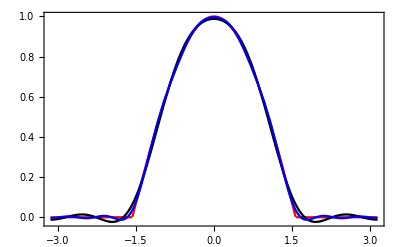

```mathematica
Plot[{f[t],f4[t],f8[t]},{t,-Pi,Pi},PlotStyle->{Red,Black,Blue}]
```